```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$1.xlsx}

```mathematica
importfile = files⟦2⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset

```mathematica
dataset=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset[All,<|"I"->(Around[#I, #dI]&),"B"-> (Around[#B, #dB] &)|>]
```

Dataset[<>]

```mathematica
line =LinearModelFit[Normal@dataset[All,{"I","B"}/*Values],{1,x},x]
```

FittedModel[-0.234132+4.60719 x]

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.234132 | 0.133064 | -1.75954 | 0.116528
x | 4.60719 | 0.0676846 | 68.0685 | 2.41518×10^-12

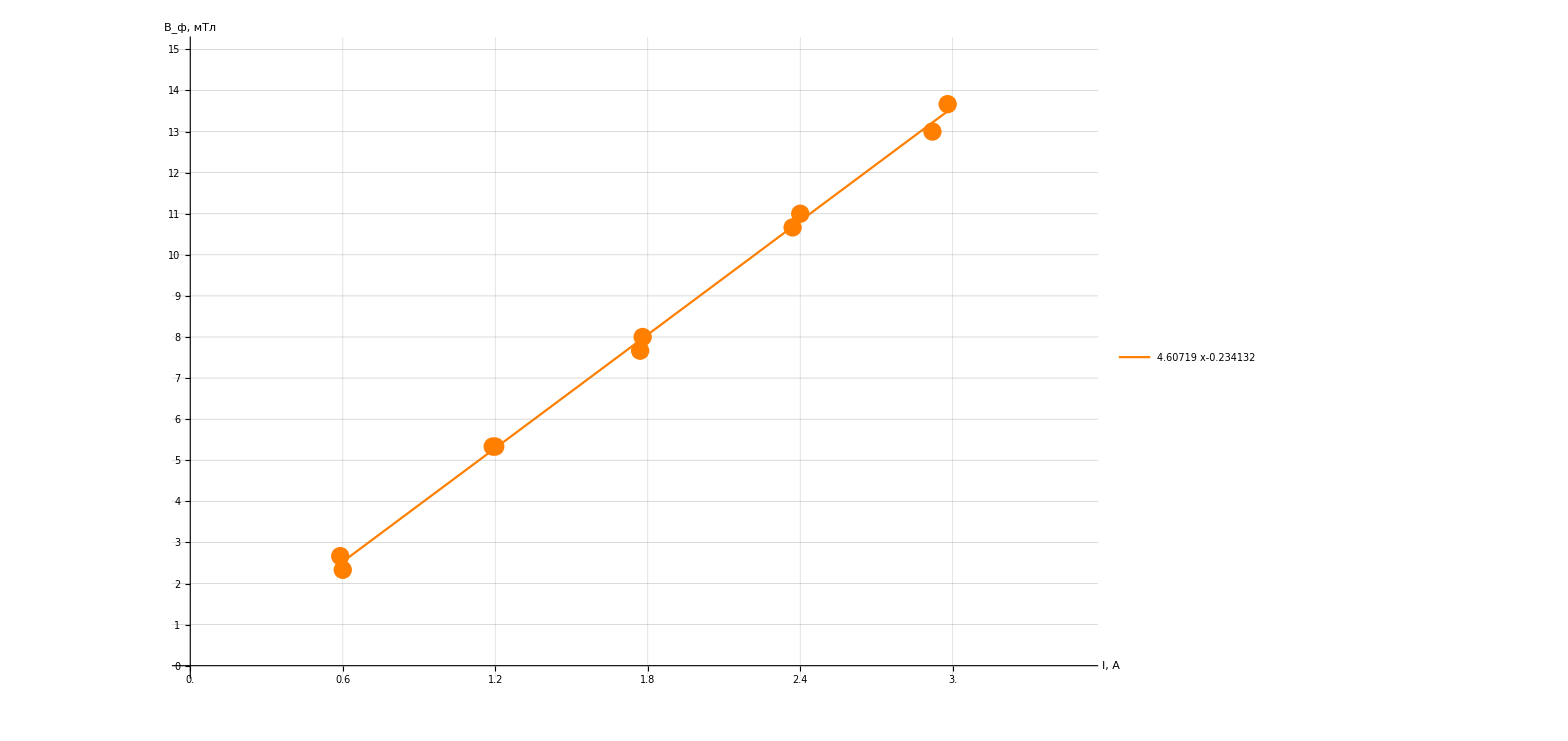

```mathematica
Show[
Plot[
{line@x},
{x,0.59, 3},
AxesLabel->{Style["I, A", Large],Style["B_(:0444), мТл",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,4,0.1],Range[0,15,1]},
PlotRange->{{0,3.5},{0,15}},
Ticks-> {Range[0,50,0.2],Range[0,15,1]},
TicksStyle->15,
PlotStyle->Orange,
PlotLegends->Placed[
LineLegend[
{Normal@line},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs},
PlotStyle->Orange
]
]
```

```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$2.xlsx}

```mathematica
importfile = files⟦3⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset

```mathematica
dataset=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset[All,<|"n"->(#n&),"B"-> (Around[#B, #dB] &)|>]
```

Dataset[<>]

```mathematica
line =LinearModelFit[Normal@dataset[All,{"n","B"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+2.34762 x]

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 2.34762 | 0.0145575 | 161.266 | 5.25758×10^-7

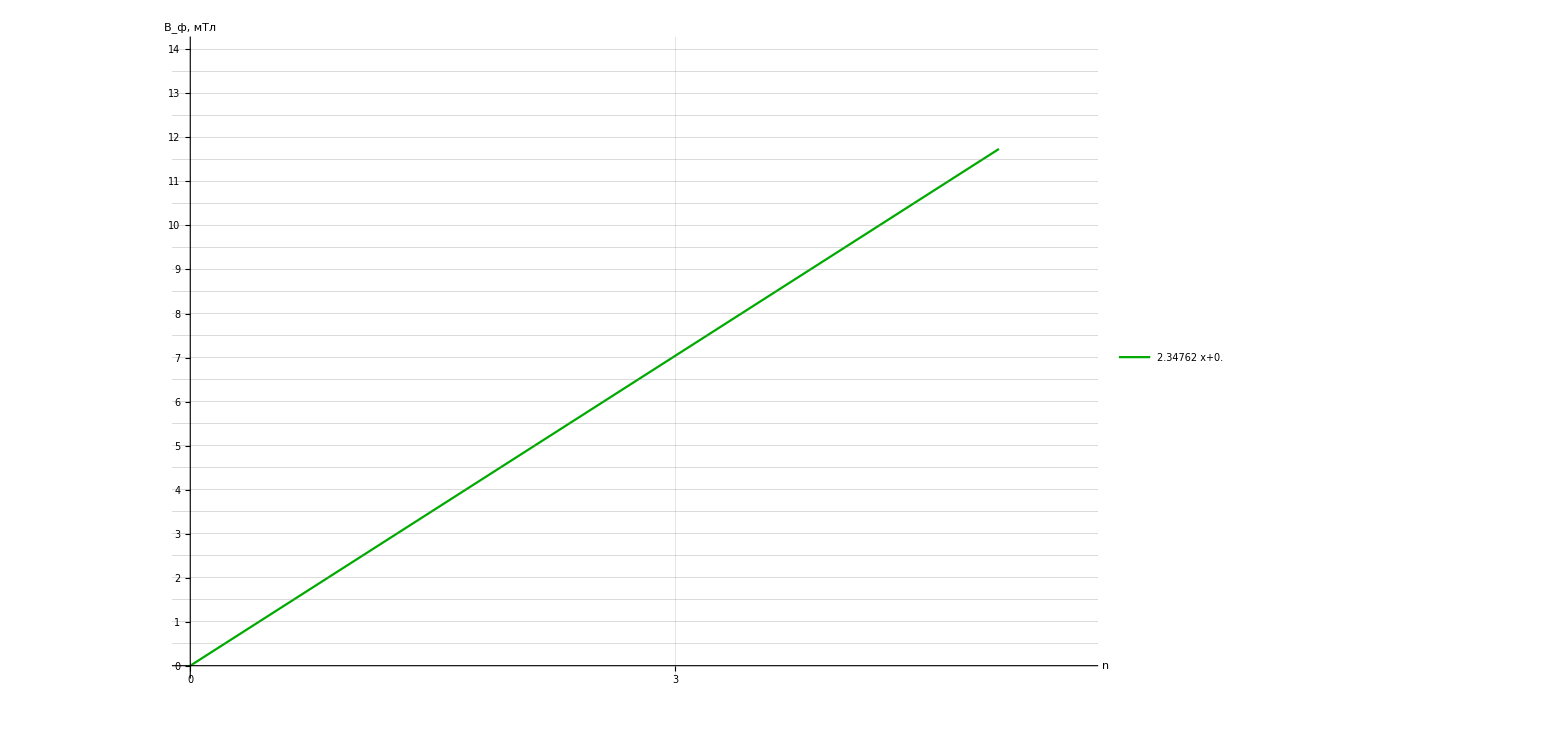

```mathematica
Show[
Plot[
{line@x},
{x,0, 5},
AxesLabel->{Style["n", Large],Style["B_(:0444), мТл",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,10,0.2],Range[0,15,0.5]},
PlotRange->{{0,5.5},{0,14}},
Ticks-> {Range[0,50,1],Range[0,15,1]},
TicksStyle->15,
PlotStyle->Darker@Green,
PlotLegends->Placed[
LineLegend[
{Normal@line},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs},
PlotStyle->Darker@Green
]
]
```